### Categorization

Tutorial

DoFun

DoFun`

DoFun/tutorial/Exporting diagrams

### Keywords

Details

# Complex fields

In DoFun the statistics of fields is determined by the two-point part of the action: If the two field labels are the same, the fields are taken as commuting, while they are treated as Grassmann fields if the two labels differ.

Since also complex fields have two different field labels additional input is required to let DoFun know that the fields commute, but have two labels.

The additional input is provided with the option specificFieldDefinitions.

doDSE[action, legs, specificFieldDefinitions→fieldDefs] | Derives the DSE corresponding to legs from action. fieldDefs contains information about the fields being commuting or anti-commuting.
doDSE[action, legs, specificFieldDefinitions→fieldDefs] | Derives the RGE corresponding to legs from action. fieldDefs contains information about the fields being commuting or anti-commuting.

Derive the DSE of complex (φ φ̄)^2 theory.

```mathematica
twoPoint=doDSE[{{φ,φb},{φb,φb,φ,φ}},{φ,φb},specificFieldDefinitions->{φ,φb}]
```

op[S[{φ,i1},{φb,i2}]]-op[S[{φb,i2},{φb,r1},{φ,i1},{φ,s1}],P[{φb,r1},{φ,s1}]]-1/2 op[S[{φb,r1},{φb,r2},{φ,i1},{φ,s1}],P[{φb,r1},{φ,s2}],P[{φb,r2},{φ,t2}],P[{φ,s1},{φb,u2}],V[{φ,s2},{φ,t2},{φb,i2},{φb,u2}]]

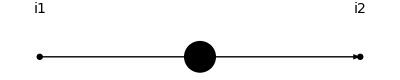
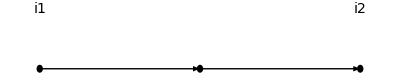
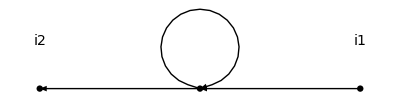
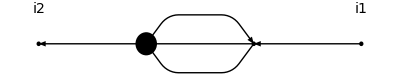
-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics--1/2^ |

```mathematica
DSEPlot[twoPoint,{{φ,Black}}]
```

More About

Related Tutorials

Related Wolfram Education Group Courses